```mathematica
HG10[x_,y_]:=(x)*ⅇ^(-(x^2+y^2))

DXHG10[x_,y_]:=(1+(x)*(-2*x))*ⅇ^(-(x^2+y^2))
DYHG10[x_,y_]:=((x)*(-2*y))*ⅇ^(-(x^2+y^2))


s:=1

a:=0.5

b:=1


HG[x_,y_,θ_]:=HG10[x*Cos[θ]-y*Sin[θ], x*Sin[θ]+y*Cos[θ]]
DXHG[x_,y_,θ_]:=DXHG10[x*Cos[θ]-y*Sin[θ], x*Sin[θ]+y*Cos[θ]]
DYHG[x_,y_,θ_]:=DYHG10[x*Cos[θ]-y*Sin[θ], x*Sin[θ]+y*Cos[θ]]
FX[x_,y_,θ_]:=-(a*HG[x,y,θ]*DXHG[x,y,θ]+s*b*HG[x,y,θ]*DYHG[x,y,θ])

FY[x_,y_,θ_]:=-(a*HG[x,y,θ]*DYHG[x,y,θ]-s*b*HG[x,y,θ]*DXHG[x,y,θ])

FXX[x_,y_,θ_]:=FX[x,y,θ]*Cos[θ]+FY[x,y,θ]*Sin[θ]
FYY[x_,y_,θ_]:=FY[x,y,θ]*Cos[θ]-FX[x,y,θ]*Sin[θ]
IHG[x_,y_,θ_]:=(Abs[HG[x,y,θ]]^2)

Manipulate[DensityPlot[IHG[x,y,θ],{x,-2,2},{y,-2,2},PlotRange->Full,PlotLegends->None],{θ,0,3.14159,Appearance->"Open"}]
Export["C:\\Users\\omatsu Lab\\Desktop\\221005_simulation\\1005_2P_intensity.avi",%]
Manipulate[VectorPlot[{FXX[x,y,θ],FYY[x,y,θ]},{x,-2,2},{y,-2,2},FrameTicks->None,VectorColorFunction->"Rainbow",VectorColorFunctionScaling->False,VectorScale->Large],{θ,0,3.14159,Appearance->"Open"}]
Export["C:\\Users\\omatsu Lab\\Desktop\\221005_simulation\\1005_2P_Rpol.avi",%]
```

C:\Users\omatsu Lab\Desktop\221005_simulation\1005_2P_Rpol.avi

```mathematica
FXXX[x_,y_]:=∑_(ii=0)^15 FXX[x,y,π*ii/16]
FYYY[x_,y_]:=∑_(ii=0)^15 FYY[x,y,π*ii/16]
```

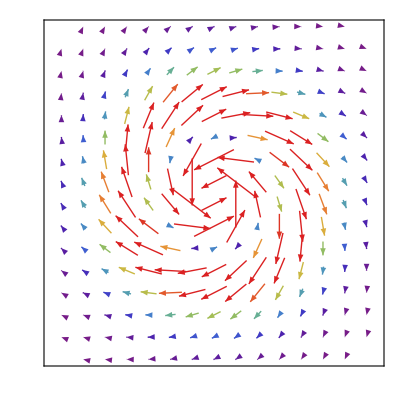

C:\Users\omatsu Lab\Desktop\221005_simulation\1005_2P_Rpol.png

```mathematica
VectorPlot[{FXXX[x,y],FYYY[x,y]},{x,-2,2},{y,-2,2},FrameTicks->None,VectorColorFunction->"Rainbow",VectorColorFunctionScaling->False,VectorScale->Large]
Export["C:\\Users\\omatsu Lab\\Desktop\\221005_simulation\\1005_2P_Rpol.png",%]
```